## Definiciones

```mathematica
SetDirectory[NotebookDirectory[]];Get["QuantumWalks.wl"]
```

```mathematica
Get["../../chaos_meets_channels/Mathematica_packages/QMB.wl"]
```

```mathematica
?QMB`*
```

```mathematica
(*moneda*)
ClearAll[c]
c[θ_,α_,ϕ_]:=FullSimplify[MatrixExp[-I*θ/2.*({Sin[α]Cos[ϕ],Sin[α]Sin[ϕ],Cos[α]}.(PauliMatrix/@{1,2,3}))]]
```

```mathematica
(*shift*)
ClearAll[S]
S[t_]:=KroneckerProduct[DiagonalMatrix[ConstantArray[1,2t],1],{{0,0},{0,1.}}]+KroneckerProduct[DiagonalMatrix[ConstantArray[1,2t],-1],{{1.,0},{0,0}}]
```

```mathematica
(*paso DTQW*)
ClearAll[U]
U[t_,θ_,α_,ϕ_]:=S[t].KroneckerProduct[IdentityMatrix[2t+1],c[θ,α,ϕ]]
```

```mathematica
(*DTQWAnalytical*)
ClearAll[DTQWAnalytical]
DTQWAnalytical[t_,θ_,α_,ϕ_]:=Fold[ArrayPad[U[#2,θ,α,ϕ].#1,2]&,{0,0,0,1,0,0},Range[t]]
DTQWAnalytical[psi0_,t_,theta_,alpha_,phi_]:=Module[{validInput},validInput=MatchQ[psi0,{_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ}];
If[!validInput,Message[DTQWAnalytical::invalidpsi0,psi0];
Return[$Failed];];
Fold[ArrayPad[U[#2,theta,alpha,phi].#1,2]&,psi0,Range[t]]]

DTQWAnalytical::invalidpsi0="ψ0 debe ser una lista de 6 elementos numéricos. Se recibió: `1`.";
```

```mathematica
(*probabilidades espacio*)
ProbDistPosition[ψ_]:=Total/@(Abs[Partition[ψ,2]]^2)
```

```mathematica
(*expected position*)
ClearAll[ExpPosition]
ExpPosition[t_,θ_,α_,ϕ_]:=ProbDistPosition[DTQWAnalytical[t,θ,α,ϕ]].Range[-t-1,t+1]
ExpPosition[ψ_]:=Module[{t=(Length[ψ]/2-3)/2},Chop[ProbDistPosition[ψ].Range[-t-1,t+1]]]
```

```mathematica
MyManipulate[t_]:=
Manipulate[
Plot[ExpPosition[t],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->30],
ImageSize->600,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |1⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->25],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

## Cálculos

```mathematica
t=5;a=0.;b=1.;
Manipulate[
Plot[Evaluate[ExpPosition[#,θ,α,ϕ]&/@Range[t]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = "<>ToString[NumberForm[a,{Infinity,1}]]<>"|0⟩+"<>ToString[NumberForm[b,{Infinity,1}]]<>"|1⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
t=5;a=1.;b=0.;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalytical[ArrayPad[{a,b},2],#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = "<>ToString[NumberForm[a,{Infinity,1}]]<>"|0⟩+"<>ToString[NumberForm[b,{Infinity,1}]]<>"|1⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

General::prng: Value of option PlotRange -> {All, {-1.05 t, 1.05 t}}
     is not All, Full, Automatic, a positive machine number, or an appropriate
     list of range specifications.

DTQWAnalytical::invalidpsi0: ψ0 debe ser una lista de 6 elementos numéricos. Se recibió: {0,0,a,b,0,0}.

Partition::pdep: Depth 1 requested in object with dimensions {}.

DTQWAnalytical::invalidpsi0: ψ0 debe ser una lista de 6 elementos numéricos. Se recibió: {0,0,a,b,0,0}.

Partition::pdep: Depth 1 requested in object with dimensions {}.

DTQWAnalytical::invalidpsi0: ψ0 debe ser una lista de 6 elementos numéricos. Se recibió: {0,0,a,b,0,0}.

General::stop: Further output of DTQWAnalytical::invalidpsi0 will be suppressed during this calculation.

Partition::pdep: Depth 1 requested in object with dimensions {}.

General::stop: Further output of Partition::pdep will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {All,{-1.05 t,1.05 t}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[$Failed,2.].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

```mathematica
t=5;a=1./√2;b=1./√2;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalytical[ArrayPad[{a,b},2],#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = "<>ToString[NumberForm[a,{Infinity,3}]]<>"|0⟩+"<>ToString[NumberForm[b,{Infinity,3}]]<>"|1⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

DTQWAnalytical::invalidpsi0: ψ0 debe ser una lista de 6 elementos numéricos. Se recibió: {0,0,a,b,0,0}.

Partition::pdep: Depth 1 requested in object with dimensions {}.

DTQWAnalytical::invalidpsi0: ψ0 debe ser una lista de 6 elementos numéricos. Se recibió: {0,0,a,b,0,0}.

Partition::pdep: Depth 1 requested in object with dimensions {}.

DTQWAnalytical::invalidpsi0: ψ0 debe ser una lista de 6 elementos numéricos. Se recibió: {0,0,a,b,0,0}.

General::stop: Further output of DTQWAnalytical::invalidpsi0 will be suppressed during this calculation.

Partition::pdep: Depth 1 requested in object with dimensions {}.

General::stop: Further output of Partition::pdep will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {All,{-1.05 t,1.05 t}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[$Failed,2.].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

```mathematica
SeedRandom[23802];
t=5;{a,b}=RandomQubitState[];
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalytical[ArrayPad[{a,b},2],#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = "<>ToString[NumberForm[a,{Infinity,3}]]<>"|0⟩+"<>ToString[NumberForm[b,{Infinity,3}]]<>"|1⟩, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

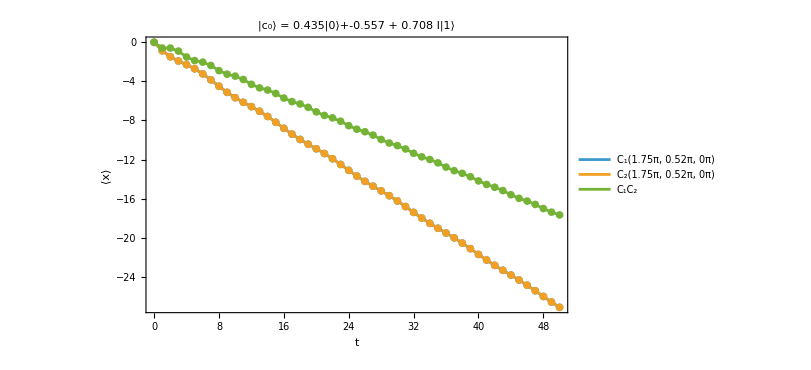

```mathematica
ψ0={a,b};tmax=50;
{θ1,α1,ϕ1}={7Pi/4.,0.52Pi,0Pi};
{θ2,α2,ϕ2}={7Pi/4.,0.52Pi,0Pi};
ListPlot[{Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[θ1,α1,ϕ1]],t]},{t,tmax}],{0,0}],Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[θ2,α2,ϕ2]],t]},{t,tmax}],{0,0}],Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[θ1,α1,ϕ1].c[θ2,α2,ϕ2]],t]},{t,tmax}],{0,0}]},
Joined->True,
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm@HoldForm[t], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->600,
PlotLegends->{"C_1("<>ToString[NumberForm[θ1/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[α1/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[ϕ1/Pi,{Infinity,2}]]<>"π)","C_2("<>ToString[NumberForm[N[θ2/Pi],{Infinity,2}]]<>"π, "<>ToString[NumberForm[α2/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[ϕ2/Pi,{Infinity,2}]]<>"π)","C_1C_2"},
PlotLabel->Style["|c_0⟩ = "<>ToString[NumberForm[a,{Infinity,3}]]<>"|0⟩+"<>ToString[NumberForm[b,{Infinity,3}]]<>"|1⟩",Black,FontSize->28],
LabelStyle->Directive[Black,FontSize->28]
]
```

```mathematica
SeedRandom[23802];
t=5;{a,b}=RandomQubitState[];
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalytical[ArrayPad[{a,b},2],#,θ,α,ϕ]]&/@Range[4,5]],{α,0,Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[α], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = "<>ToString[NumberForm[a,{Infinity,3}]]<>"|0⟩+"<>ToString[NumberForm[b,{Infinity,3}]]<>"|1⟩, θ = "<>ToString[NumberForm[θ/Pi,{Infinity,2}]]<>"π, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{θ,0,2Pi},{ϕ,0,2Pi}]
```

```mathematica
b
```

-0.556655+0.70778 ⅈ

```mathematica
t=5;
SeedRandom[23802];
t=5;{a,b}=RandomQubitState[];
Manipulate[Plot[ExpPosition[DTQWAnalytical[ArrayPad[{a,b},2],5,θ,α,ϕ]],{α,0,Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[α], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,4}],Automatic}},
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = "<>ToString[NumberForm[a,{Infinity,3}]]<>"|0⟩+"<>ToString[NumberForm[b,{Infinity,3}]]<>"|1⟩, θ = "<>ToString[NumberForm[θ/Pi,{Infinity,2}]]<>"π, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π",Black,FontSize->28]
],{θ,0,2Pi},{ϕ,0,2Pi}]
```

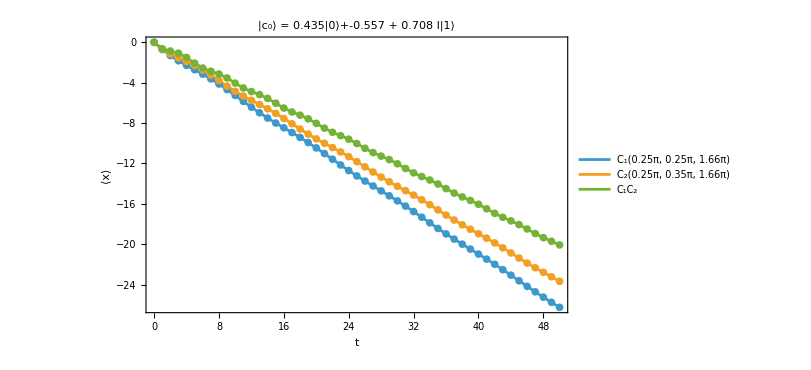

```mathematica
ψ0={a,b};tmax=50;
{θ1,α1,ϕ1}={Pi/4.,Pi/4.,1.66Pi};
{θ2,α2,ϕ2}={Pi/4.,Pi/4+0.1Pi,1.66Pi};
ListPlot[{Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[θ1,α1,ϕ1]],t]},{t,tmax}],{0,0}],Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[θ2,α2,ϕ2]],t]},{t,tmax}],{0,0}],Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[θ1,α1,ϕ1].c[θ2,α2,ϕ2]],t]},{t,tmax}],{0,0}]},
Joined->True,
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm@HoldForm[t], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->600,
PlotLegends->{"C_1("<>ToString[NumberForm[θ1/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[α1/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[ϕ1/Pi,{Infinity,2}]]<>"π)","C_2("<>ToString[NumberForm[N[θ2/Pi],{Infinity,2}]]<>"π, "<>ToString[NumberForm[α2/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[ϕ2/Pi,{Infinity,2}]]<>"π)","C_1C_2"},
PlotLabel->Style["|c_0⟩ = "<>ToString[NumberForm[a,{Infinity,3}]]<>"|0⟩+"<>ToString[NumberForm[b,{Infinity,3}]]<>"|1⟩",Black,FontSize->28],
LabelStyle->Directive[Black,FontSize->28]
]
```